FRET histogram fitting

Load some datapaclet:Fretica/tutorial/FRETHistogramFitting#432517435 | Fitting with constraintspaclet:Fretica/tutorial/FRETHistogramFitting#186252503
FMakeModel[model] and  FFindGuess[dat,model]paclet:Fretica/tutorial/FRETHistogramFitting#406679658 | Fitting with fixed parameterspaclet:Fretica/tutorial/FRETHistogramFitting#511454635
FFitFretHistogram[dat, model, guess] paclet:Fretica/tutorial/FRETHistogramFitting#251117578 | Getting the peaks integrals: FFRETPeakIntegratepaclet:Fretica/tutorial/FRETHistogramFitting#106253524
FFitFretHistogram[dat, model, peakestimates] paclet:Fretica/tutorial/FRETHistogramFitting#365205158 | FDetermineShotNoiseWidthspaclet:Fretica/tutorial/FRETHistogramFitting#261672841
FFitFretHistogram[{Emin,Emax,ΔE},model,peakestimates] paclet:Fretica/tutorial/FRETHistogramFitting#105914983 | Global fitting of multiple histogramspaclet:Fretica/tutorial/FRETHistogramFitting#51573926
Using the FSubPopStyle and FSubPopOptionspaclet:Fretica/tutorial/FRETHistogramFitting#326528958 |

```mathematica
Needs["Fretica`"]
```

```mathematica
?FFitFretHistogram
```

Load some data

```mathematica
(*typical settings for a two channel FRET measurement*)
FEnablePie[False];
FSetFRETRoutes[{"A","D"}](* detector1: acceptor, detector2: donor*)
FSetRCM[({{1, -0.08}, {0, 1.5}})];(*γ=1.5, Subscript[β, D->A]=0.08, Subscript[β, A->D]=0.*)
FSetDirectAcceptorExcitation[0.04];
FOpenTTTR[$FreticaExamples<>"\\Sim02.ht3"]  ;
FDetermineBackground[];(*returns estimated background rates in counts per seconds*)
FFindBurstsDeltaT[0.00015,50,10000];
```

FMakeModel[model] and  FFindGuess[dat,model]

```mathematica
?FMakeFRETPeakModel
?FFindGuess
```

FMakeModel is used by the functions FFindGuess, FFitFretHistogram and FPlotFRETFit
It defines the model and the model parameters

```mathematica
{peaks,params}=FMakeFRETPeakModel[{"L","G","L"}];
peaks[[1]][e]
peaks[[2]][e]
peaks[[3]][e]
params
```

Piecewise[{{2^(-(Log[1+((-1+Asym[1]^2) (e-Pos[1]))/(Asym[1] Width[1])]^2)/Log[Asym[1]]^2) Abs[Ampl[1]], ((-1+Asym[1]^2) (e-Pos[1]))/(Asym[1] Width[1])>-1}, {0, True}}]

ⅇ^(-(e-Pos[2])^2/(2 Width[2]^2)) Abs[Ampl[2]]

Piecewise[{{2^(-(Log[1+((-1+Asym[3]^2) (e-Pos[3]))/(Asym[3] Width[3])]^2)/Log[Asym[3]]^2) Abs[Ampl[3]], ((-1+Asym[3]^2) (e-Pos[3]))/(Asym[3] Width[3])>-1}, {0, True}}]

{{Pos[1],Ampl[1],Width[1],Asym[1]},{Pos[2],Ampl[2],Width[2]},{Pos[3],Ampl[3],Width[3],Asym[3]}}

```mathematica
Through[peaks[e]]
```

{Piecewise[{{2^(-(Log[1+((-1+Asym[1]^2) (e-Pos[1]))/(Asym[1] Width[1])]^2)/Log[Asym[1]]^2) Abs[Ampl[1]], ((-1+Asym[1]^2) (e-Pos[1]))/(Asym[1] Width[1])>-1}, {0, True}}],ⅇ^(-(e-Pos[2])^2/(2 Width[2]^2)) Abs[Ampl[2]],Piecewise[{{2^(-(Log[1+((-1+Asym[3]^2) (e-Pos[3]))/(Asym[3] Width[3])]^2)/Log[Asym[3]]^2) Abs[Ampl[3]], ((-1+Asym[3]^2) (e-Pos[3]))/(Asym[3] Width[3])>-1}, {0, True}}]}

```mathematica
peaktotal[e_]=Total@Through[peaks[e]]
```

ⅇ^(-(e-Pos[2])^2/(2 Width[2]^2)) Abs[Ampl[2]]+(Piecewise[{{2^(-(Log[1+((-1+Asym[1]^2) (e-Pos[1]))/(Asym[1] Width[1])]^2)/Log[Asym[1]]^2) Abs[Ampl[1]], ((-1+Asym[1]^2) (e-Pos[1]))/(Asym[1] Width[1])>-1}, {0, True}}])+(Piecewise[{{2^(-(Log[1+((-1+Asym[3]^2) (e-Pos[3]))/(Asym[3] Width[3])]^2)/Log[Asym[3]]^2) Abs[Ampl[3]], ((-1+Asym[3]^2) (e-Pos[3]))/(Asym[3] Width[3])>-1}, {0, True}}])

FFindGuess[dat,model,peakestimates] automatically estimates initial parameters for the fit.
Input: the fret histogram (dat), model ({"L", "G", "L",...}) and a list of peak position guesses either in form of a value or by a range {posmin, posmax}. In the later case the FRET value where the histogram is maximal on the range {posmin, posmax} is used as initial guess of the peak position.

```mathematica
dat=FParamHisto["E",{-0.2,1.2,0.03},FOutput->FData];
guess=FFindGuess[dat,{"G","G","L"},{{-1.0,0.2},0.5,{0.6,1}}]
```

{{Pos[1],-0.035},{Ampl[1],207},{Width[1],0.12},{Pos[2],0.5},{Ampl[2],118},{Width[2],0.12},{Pos[3],0.655},{Ampl[3],130},{Width[3],0.12},{Asym[3],0.9}}

FFitFretHistogram[dat, model, guess]

```mathematica
dat=FParamHisto["E",{-0.2,1.2,0.03},FOutput->FData];
guess=FFindGuess[dat,model={"G","G","L"},{{-1.0,0.2},0.45,0.72}];
{fitparams,fitplot,fitttedmodel}=FFitFretHistogram[dat,model,guess]
```

-Graphics-

```mathematica
fitttedmodel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
Pos[1] | -0.0421488 | 0.00117084 | -35.9988 | 7.93003×10^-30
Ampl[1] | 212.928 | 5.43727 | 39.1608 | 4.12058×10^-31
Width[1] | 0.039708 | 0.00117084 | 33.9142 | 6.39558×10^-29
Pos[2] | 0.488059 | 0.0131788 | 37.0335 | 2.93477×10^-30
Ampl[2] | 124.422 | 9.22556 | 13.4867 | 1.21041×10^-15
Width[2] | 0.082148 | 0.00815657 | 10.0714 | 5.1354×10^-12
Pos[3] | 0.692164 | 0.00644702 | 107.362 | 9.99747×10^-47
Ampl[3] | 124.452 | 6.03709 | 20.6145 | 1.60328×10^-21
Width[3] | 0.162535 | 0.0228835 | 7.1027 | 2.40838×10^-8
Asym[3] | 0.913511 | 0.156306 | 5.84439 | 1.12178×10^-6

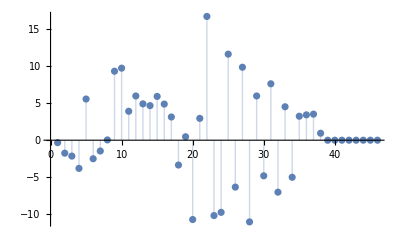

```mathematica
ListPlot[fitttedmodel["FitResiduals"],Filling->Axis]
```

FFitFretHistogram[dat, model, peakestimates]

```mathematica
dat=FParamHisto["E",{-0.2,1.2,0.03},FOutput->FData];
FFitFretHistogram[dat,{"G","G","L"},{{-1.0,0.2},0.5,0.7}]
```

-Graphics-

FFitFretHistogram[{Emin,Emax,ΔE},model,peakestimates]

```mathematica
fitresult=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","L"},{{-1.0,0.2},0.5,0.7}]
```

-Graphics-

Note that the graphical output is completely customizable using options. Examples are given below.

```mathematica
FFRETPeakIntegrate[{"G","G","L"},fitresult[[1]],{-0.1,1.2}]
```

{13.197,17.6144,13.8799}

#### Using FFitCurveStyle and FFitCurveOptions

The FFitCurveStyle option can be  used to change the plot style of the main fitting curve

```mathematica
FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","L"},{{-1.0,0.2},0.5,0.7},FFitCurveStyle->{Blue,AbsoluteThickness[3]}]
```

-Graphics-

More general changes can be achieved with FFitCurveOptions

```mathematica
FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","L"},{{-1.0,0.2},0.5,0.7},FFitCurveOptions->{Filling->Bottom, PlotStyle->{Blue,AbsoluteThickness[3]}}]
```

-Graphics-

Using the FSubPopStyle and FSubPopOptions

The FSubPopStyle option is used to change the plot style of the subpopulation curves

```mathematica
FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","L"},{{-1.0,0.2},0.5,0.7},FSubPopStyle->{Blue,Darker@Green,Red}]
```

-Graphics-

The FSubPopOptions option  is more general

```mathematica
FFitFretHistogram[{-0.2,1.0,0.02},{"L","G","L"},{{-1.0,0.2},0.5,0.7},FSubPopOptions->{Filling->Bottom,PlotStyle->{Blue,Darker@Green,Red}}]
```

-Graphics-

Fitting with constraints

Note that constraints and guess values must not conflict.

```mathematica
fitresult=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{-0.1,0.5,0.7},FConstraints->{Width[2]==Width[3]}]
```

-Graphics-

```mathematica
FFRETPeakIntegrate[{"G","G","G"},fitresult[[1]],{-0.1,1.2}]
```

{13.197,15.6906,15.9039}

Fitting with fixed parameters

```mathematica
FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{-0.1,0.5,0.7},FFixParams->{Pos[1]->0.0}]
```

-Graphics-

Note that this is a bad example tor the use of the FFixParams option, because the donor-only peak is (as expected) not located at E=0 but at a negative value.

Getting the peaks integrals: FFRETPeakIntegrate

```mathematica
?FFRETPeakIntegrate
```

```mathematica
fitresult=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","L"},{{-1.0,0.2},0.5,0.7}]
```

-Graphics-

```mathematica
FFRETPeakIntegrate[{"G","G","L"},fitresult[[1]],{-0.1,1.2}]
```

{13.197,17.6144,13.8799}

FDetermineShotNoiseWidths

```mathematica
FDetermineShotNoiseWidths[{-0.2,1.2,0.03},{"G","G","G"},{{-0.1,0.2},0.5,0.7}]
```

-Graphics-

Global fitting of multiple histograms

All commands in the above sub sections are also generalized to allow for global fitting of multiple histograms which are combined in a list.

Here a list of for histograms is loaded

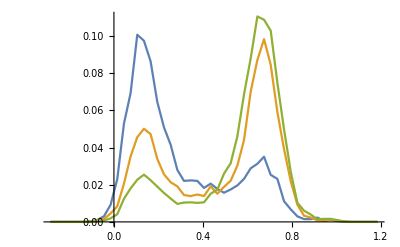

```mathematica
SetDirectory[NotebookDirectory[]];
histograms=<<($FreticaExamples<>"\\histograms");
ListPlot[histograms,Joined->True]
```

A global model for four histograms with global parameters for the widths:

```mathematica
FMakeFRETPeakModel[{"G","G","G"},4,{Pos[1],Pos[2],Pos[3]}]
```

{{{Function[{e$},FGaussian[e$,Pos[1],Ampl[1,1],Width[1,1]]],Function[{e$},FGaussian[e$,Pos[2],Ampl[1,2],Width[1,2]]],Function[{e$},FGaussian[e$,Pos[3],Ampl[1,3],Width[1,3]]]},{Function[{e$},FGaussian[e$,Pos[1],Ampl[2,1],Width[2,1]]],Function[{e$},FGaussian[e$,Pos[2],Ampl[2,2],Width[2,2]]],Function[{e$},FGaussian[e$,Pos[3],Ampl[2,3],Width[2,3]]]},{Function[{e$},FGaussian[e$,Pos[1],Ampl[3,1],Width[3,1]]],Function[{e$},FGaussian[e$,Pos[2],Ampl[3,2],Width[3,2]]],Function[{e$},FGaussian[e$,Pos[3],Ampl[3,3],Width[3,3]]]},{Function[{e$},FGaussian[e$,Pos[1],Ampl[4,1],Width[4,1]]],Function[{e$},FGaussian[e$,Pos[2],Ampl[4,2],Width[4,2]]],Function[{e$},FGaussian[e$,Pos[3],Ampl[4,3],Width[4,3]]]}},{Pos[1],Ampl[1,1],Width[1,1],Pos[2],Ampl[1,2],Width[1,2],Pos[3],Ampl[1,3],Width[1,3],Ampl[2,1],Width[2,1],Ampl[2,2],Width[2,2],Ampl[2,3],Width[2,3],Ampl[3,1],Width[3,1],Ampl[3,2],Width[3,2],Ampl[3,3],Width[3,3],Ampl[4,1],Width[4,1],Ampl[4,2],Width[4,2],Ampl[4,3],Width[4,3]}}

Note that not global parameters are now of the form paramname[i,j] where i is the number of the histogram and j is the peak number. Global parameters have only the peak number as index.

Finding initial guesses for fitting with a global model:

```mathematica
FFindGuess[histograms,{"G","G","G"},{Pos[1],Pos[2],Pos[3]},{0.1,0.4,0.7}]
```

{{Pos[1],0.1},{Ampl[1,1],0.100786},{Width[1,1],0.12},{Pos[2],0.4},{Ampl[1,2],0.0182877},{Width[1,2],0.12},{Pos[3],0.7},{Ampl[1,3],0.0253319},{Width[1,3],0.12},{Ampl[2,1],0.0456048},{Width[2,1],0.12},{Ampl[2,2],0.0139157},{Width[2,2],0.12},{Ampl[2,3],0.0845963},{Width[2,3],0.12},{Ampl[3,1],0.0226993},{Width[3,1],0.12},{Ampl[3,2],0.0105292},{Width[3,2],0.12},{Ampl[3,3],0.102967},{Width[3,3],0.12}}

The above commands are internally used in the following global fit, where beside the three peak positions also the width of the second peak are global fit parameters. In addition Width[2] is fixed to a value of 0.1.

```mathematica
fit=FFitFretHistogram[histograms,{"G","G","G"},{Pos[1],Pos[2],Pos[3],Width[2]},{0.1,0.4,0.7},FFixParams->{Width[2]->0.1}]
```

-Graphics-

Plot amplitudes of peak one and three:

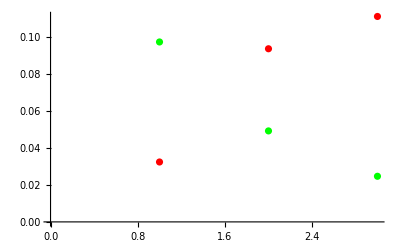

```mathematica
ListPlot[Table[{Ampl[i,1],Ampl[i,3]},{i,Length[histograms]}]ᵀ/.fit[[1]],PlotStyle->{Green,Red}]
```

FFRETPeakIntegrate does now return the peak integrals for each histogram combined in a list.

```mathematica
FFRETPeakIntegrate[{"G","G","G"},fit[[1]],{-0.2,1.2}]
```

{{0.0181741,0.00566566,0.00621614},{0.00868009,0.00435702,0.0167338},{0.00441782,0.00348214,0.0221031}}

```mathematica
fit[[3]]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
Pos[1] | 0.133278 | 0.00126724 | 105.172 | 3.7196×10^-129
Ampl[1,1] | 0.0975483 | 0.00146055 | 66.7887 | 1.28319×10^-103
Width[1,1] | 0.0743265 | 0.00143711 | 51.7193 | 1.68337×10^-89
Pos[2] | 0.395025 | 0.00690051 | 57.2458 | 4.49851×10^-95
Ampl[1,2] | 0.0226027 | 0.00113632 | 19.8911 | 1.53113×10^-41
Pos[3] | 0.667296 | 0.000929355 | 718.021 | 6.04442×10^-239
Ampl[1,3] | 0.0324774 | 0.00144156 | 22.5293 | 4.56507×10^-47
Width[1,3] | 0.0763571 | 0.0042936 | 17.7839 | 7.44063×10^-37
Ampl[2,1] | 0.0493273 | 0.00150182 | 32.8451 | 2.191×10^-65
Width[2,1] | 0.0702017 | 0.00264046 | 26.5869 | 7.44096×10^-55
Ampl[2,2] | 0.017382 | 0.00110105 | 15.7868 | 3.4005×10^-32
Ampl[2,3] | 0.0938684 | 0.00149246 | 62.8953 | 2.80082×10^-100
Width[2,3] | 0.0711188 | 0.0013862 | 51.3049 | 4.63087×10^-89
Ampl[3,1] | 0.0247327 | 0.00149092 | 16.5889 | 4.3205×10^-34
Width[3,1] | 0.07126 | 0.00523591 | 13.6099 | 6.64852×10^-27
Ampl[3,2] | 0.0138917 | 0.00112741 | 12.3218 | 1.07248×10^-23
Ampl[3,3] | 0.111376 | 0.00141631 | 78.6382 | 9.42321×10^-113
Width[3,3] | 0.0791718 | 0.00124479 | 63.6023 | 6.71087×10^-101

| Related Guides
▪Fretica